```mathematica
Integrate[r/Sqrt[r0^4-r^4],r]
```

-1/2 ArcTan[(r^2 √(-r^4+r0^4))/(r^4-r0^4)]

```mathematica
Integrate[1/Sqrt[a^2-x^2],x]
```

-ArcTan[(x √(a^2-x^2))/(-a^2+x^2)]

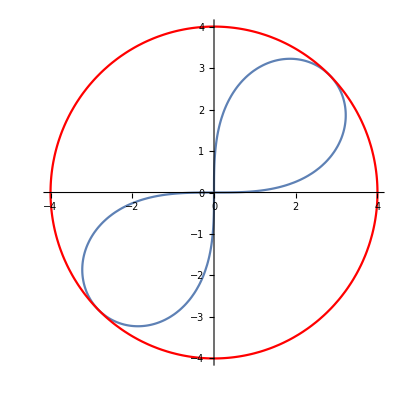

```mathematica
Show[PolarPlot[4Sqrt[Sin[2θ]],{θ,0,2Pi}],PolarPlot[4,{θ,0,2Pi},PlotStyle->Red]]
```

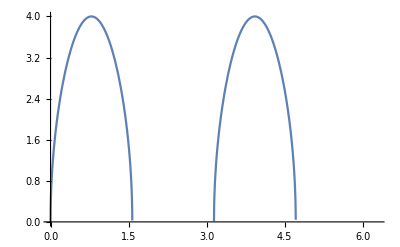

```mathematica
Plot[4Sqrt[Sin[2θ]],{θ,0,2Pi}]
```

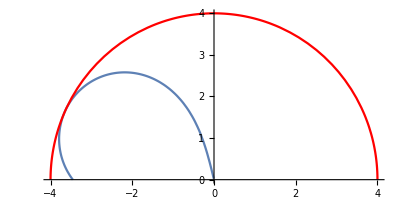

```mathematica
Show[PolarPlot[4Sqrt[Sin[2θ Sin[5Pi/3]]],{θ,0,Pi}],PolarPlot[4,{θ,0,Pi},PlotStyle->Red]]
```

```mathematica
Manipulate[ParametricPlot3D[{4Sqrt[Sin[2ϕ]]Sin[ϕ]Cos[θ],4Sqrt[Sin[2ϕ]]Sin[ϕ]Sin[θ],4Sqrt[Sin[2ϕ]]Cos[ϕ]},{ϕ,0,Pi}],{θ,0,2Pi}]
```

```mathematica
Manipulate[ParametricPlot3D[{4Sqrt[Sin[2θ Sin[ϕ]]]Sin[ϕ]Cos[θ],4Sqrt[Sin[2θ Sin[ϕ]]]Sin[ϕ]Sin[θ],4Sqrt[Sin[2θ Sin[ϕ]]]Cos[ϕ]},{θ,0,2Pi}],{ϕ,0,Pi}]
```

```mathematica
Show[
Table[ParametricPlot3D[{4Sqrt[Sin[2ϕ]]Sin[ϕ]Cos[θ],4Sqrt[Sin[2ϕ]]Sin[ϕ]Sin[θ],4Sqrt[Sin[2ϕ]]Cos[ϕ]},{ϕ,0,2Pi}],{θ,0,2Pi,Pi/50}],
Table[ParametricPlot3D[{4Sqrt[Sin[2θ Sin[ϕ]]]Sin[ϕ]Cos[θ],4Sqrt[Sin[2θ Sin[ϕ]]]Sin[ϕ]Sin[θ],4Sqrt[Sin[2θ Sin[ϕ]]]Cos[ϕ]},{θ,0,2Pi},PlotStyle->Red],{ϕ,0,Pi,Pi/50}],PlotRange->All
]
```

-Graphics3D-

```mathematica
Integrate[1/Sqrt[r^2+n^2],r]
```

Log[r+√(n^2+r^2)]

```mathematica
Manipulate[
ParametricPlot3D[{ρ Sinh[Log[(ρ+Sqrt[ρ^2+25])/5]]Cos[ϕ0],ρ Sinh[Log[(ρ+Sqrt[ρ^2+25])/5]]Sin[ϕ0],ρ Cosh[Log[(ρ+Sqrt[ρ^2+25])/5]]},{ρ,0,10}],{ϕ0,0,2Pi}
]
```

```mathematica
Manipulate[
ParametricPlot3D[{ρ Sin[θ0]Cosh[1/Sin[θ0]Log[(ρ+Sqrt[ρ^2+25])/5]],ρ Sin[θ0]Sinh[1/Sin[θ0]Log[(ρ+Sqrt[ρ^2+25])/5]],ρ Cos[θ0]},{ρ,0,10}],{θ0,Pi/3,Pi}
]
```

```mathematica
Show[
Table[ParametricPlot3D[{ρ Sinh[Log[(ρ+Sqrt[ρ^2+25])/5]]Cos[ϕ0],ρ Sinh[Log[(ρ+Sqrt[ρ^2+25])/5]]Sin[ϕ0],ρ Cosh[Log[(ρ+Sqrt[ρ^2+25])/5]]},{ρ,0,10}],{ϕ0,0,2Pi,Pi/200}],
Table[ParametricPlot3D[{ρ Sin[θ0]Cosh[1/Sin[θ0]Log[(ρ+Sqrt[ρ^2+25])/5]],ρ Sin[θ0]Sinh[1/Sin[θ0]Log[(ρ+Sqrt[ρ^2+25])/5]],ρ Cos[θ0]},{ρ,0,10},PlotStyle->Red],{θ0,0.01,2Pi,Pi/200}],PlotRange->Full
]
```

-Graphics3D-

```mathematica
Integrate[r/Sqrt[r^4+r0^4],r]
```

1/2 Log[r^2+√(r^4+r0^4)]

```mathematica
Solve[r^2+Sqrt[r^4+r0^4]==r01^2 Sin[2ϕ],r]
```

{{r→-(√(-r0^4 Csc[2 ϕ]+r01^4 Sin[2 ϕ]))/(√2 r01)},{r→(√(-r0^4 Csc[2 ϕ]+r01^4 Sin[2 ϕ]))/(√2 r01)}}

```mathematica
Show[
Table[ParametricPlot3D[{ρ Sinh[Log[(ρ^2+Sqrt[ρ^4+625])/25]]Cos[ϕ0],ρ Sinh[Log[(ρ^2+Sqrt[ρ^4+625])/25]]Sin[ϕ0],ρ Cosh[Log[(ρ^2+Sqrt[ρ^4+625])/25]]},{ρ,0,5}],{ϕ0,0,2Pi,Pi/200}],PlotRange->Full
]
```

-Graphics3D-

```mathematica
Integrate[1/Sqrt[r^6+C1 r^2],r]
```

-(r √(C1+r^4) ArcTanh[(√(C1+r^4))/(√C1)])/(2 √C1 √(r^2 (C1+r^4)))

```mathematica
FullSimplify[Tanh[x]^2-1]
```

-Sech[x]^2

```mathematica
Integrate[1/Sqrt[r0^4+λ^4 Exp[-α ϕ]],ϕ]
```

(2 ⅇ^(-(α ϕ)/2) √(ⅇ^(α ϕ) r0^4+λ^4) Log[ⅇ^((α ϕ)/2) r0^4+r0^2 √(ⅇ^(α ϕ) r0^4+λ^4)])/(r0^2 α √(r0^4+ⅇ^(-α ϕ) λ^4))

```mathematica
Sum[(Kb E^(-S+I θ)T1)^n,{n,0,Infinity}]
```

ⅇ^S/(ⅇ^S-ⅇ^(ⅈ θ) Kb T1)

```mathematica
Sum[(Kb E^(-S-I θ)T1)^n,{n,0,Infinity}]
```

ⅇ^(S+ⅈ θ)/(ⅇ^(S+ⅈ θ)-Kb T1)

```mathematica
FullSimplify[Sum[(Kb E^(-S+I θ)T1)^n,{n,0,Infinity}]Sum[(Kb E^(-S-I θ)T1)^n,{n,0,Infinity}]]
```

ⅇ^(2 S+ⅈ θ)/((ⅇ^(S+ⅈ θ)-Kb T1) (ⅇ^S-ⅇ^(ⅈ θ) Kb T1))

```mathematica
Sum[1/N1!/N1! (K1 T Exp[-S0 T])^(2N1),{N1,0,Infinity}]
```

BesselI[0,2 ⅇ^(-S0 T) K1 T]

```mathematica
Sum[Exp[-n^2 T1/2/A1],{n,0,Infinity}]
```

1/2 (1+EllipticTheta[3,0,ⅇ^(-T1/(2 A1))])

```mathematica
Integrate[Exp[-λ Cos[θ]],{θ,0,2Pi}]
```

2 π BesselI[0,λ]

```mathematica
Integrate[1/Sqrt[Exp[-β ϕ]-Exp[-β ϕ0]],ϕ]
```

(2 ⅇ^(-(β ϕ)/2) √(-ⅇ^(β ϕ)+ⅇ^(β ϕ0)) ArcTan[ⅇ^((β ϕ)/2)/(√(-ⅇ^(β ϕ)+ⅇ^(β ϕ0)))])/(√(ⅇ^(-β ϕ)-ⅇ^(-β ϕ0)) β)

```mathematica
Integrate[1/r/Sqrt[r^4- r0^4],r]
```

-ArcTanh[(√(r^4-r0^4))/(√(-r0^4))]/(2 √(-r0^4))

```mathematica
Integrate[1/r/Sqrt[r0^4- r^4],r]
```

-ArcTanh[(√(-r^4+r0^4))/(√(r0^4))]/(2 √(r0^4))

```mathematica
Integrate[1/Sqrt[1-Exp[β(ϕ0-ϕ)]],ϕ]
```

(2 ArcTanh[√(1-ⅇ^(-β ϕ+β ϕ0))])/β

```mathematica
N[Cosh[ArcTanh[1]]]
```

∞

```mathematica
Integrate[1/r/Sqrt[r^4+r0^4],r]
```

-ArcTanh[(√(r^4+r0^4))/(√(r0^4))]/(2 √(r0^4))

```mathematica
Integrate[Exp[β ϕ/2]/Sqrt[1+Exp[β(ϕ-ϕ0)]],ϕ]
```

(2 ⅇ^((β ϕ0)/2) ArcSinh[ⅇ^(1/2 β (ϕ-ϕ0))])/β

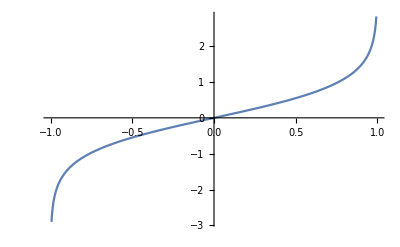

```mathematica
Plot[ArcTanh[x],{x,-1,1}]
```

```mathematica
Reduce[-1<-Sqrt[1+x^4]<0,x]
```

False

```mathematica
Plot[Sinh[3ArcTanh[Sqrt[1+x^4]]],{x,-1,1}]
```

-Graphics-

```mathematica
Reduce[Sinh[-β/2Sqrt[3/2]ArcTanh[Sqrt[1+x^4]]]∈ Reals,{x,β}]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Sinh[1/2 √(3/2) β ArcTanh[√(1+x^4)]]∈ℝ,{x,β}]

```mathematica
Integrate[1/Sqrt[Exp[-β ϕ]-Exp[-β ϕ0]],ϕ]
```

(2 ⅇ^(-(β ϕ)/2) √(-ⅇ^(β ϕ)+ⅇ^(β ϕ0)) ArcTan[ⅇ^((β ϕ)/2)/(√(-ⅇ^(β ϕ)+ⅇ^(β ϕ0)))])/(√(ⅇ^(-β ϕ)-ⅇ^(-β ϕ0)) β)

```mathematica
Integrate[1/r/Sqrt[r^4-r0^4],r]
```

-ArcTanh[(√(r^4-r0^4))/(√(-r0^4))]/(2 √(-r0^4))

```mathematica
Collect[FullSimplify[(4x^3+3(2A-B1-C1)x^2+2x(A^2+B1 C1-2A(B1+C1))+(2A B1 C1-A^2(B1+C1)))/(x+A)],x]
```

-A B1-A C1+2 B1 C1+(2 A-3 (B1+C1)) x+4 x^2

```mathematica
Simplify[Expand[(2A-B1-C1)/9-2/3(3B1 C1+A B1+A C1-2A^2)]]
```

1/9 (12 A^2+A (2-6 B1-6 C1)-C1-B1 (1+18 C1))

```mathematica
Expand[12 A^2+A (2-6 B1-6 C1)-C1-B1 (1+18 C1)]
```

2 A+12 A^2-B1-6 A B1-C1-6 A C1-18 B1 C1

```mathematica
Integrate[(x+A)Sqrt[x^2-(B1+C1)x+B1 C1],x]
```

(√((-B1+x) (-C1+x)) ((B1-C1) (2 A+B1+C1) √(-B1+x)+2/3 (6 A+7 B1-C1) (-B1+x)^(3/2)+8/3 (-B1+x)^(5/2)-((B1-C1)^2 (2 A+B1+C1) Log[√(-B1+x)+√(-C1+x)])/(√(-C1+x))))/(8 √(-B1+x))

```mathematica
FullSimplify[(√(-C1+x) ((B1-C1) (2 A+B1+C1) √(-B1+x)+2/3 (6 A+7 B1-C1) (-B1+x)^(3/2)+8/3 (-B1+x)^(5/2)-((B1-C1)^2 (2 A+B1+C1) Log[√(-B1+x)+√(-C1+x)])/(√(-C1+x))))/8]
```

-1/24 √(-B1+x) √(-C1+x) (3 B1^2-2 B1 C1+3 C1^2+6 A (B1+C1-2 x)+2 (B1+C1) x-8 x^2)-1/8 (B1-C1)^2 (2 A+B1+C1) Log[√(-B1+x)+√(-C1+x)]

```mathematica
FullSimplify[Limit[-1/24 √(-B1+x) √(-C1+x) (3 B1^2-2 B1 C1+3 C1^2+6 A (B1+C1-2 x)+2 (B1+C1) x-8 x^2)-1/8 (B1-C1)^2 (2 A+B1+C1) Log[√(-B1+x)+√(-C1+x)],x->-A]]
```

-1/24 √(-A-B1) √(-A-C1) (4 A^2+3 B1^2-2 B1 C1+3 C1^2+4 A (B1+C1))-1/8 (B1-C1)^2 (2 A+B1+C1) Log[√(-A-B1)+√(-A-C1)]

```mathematica
FullSimplify[Limit[-1/24 √(-B1+x) √(-C1+x) (3 B1^2-2 B1 C1+3 C1^2+6 A (B1+C1-2 x)+2 (B1+C1) x-8 x^2)-1/8 (B1-C1)^2 (2 A+B1+C1) Log[√(-B1+x)+√(-C1+x)],x->B1]]
```

-1/16 (B1-C1)^2 (2 A+B1+C1) Log[B1-C1]

```mathematica
FullSimplify[(-1/16 (B1-C1)^2 (2 A+B1+C1) Log[B1-C1])-(-1/24 √(-A-B1) √(-A-C1) (4 A^2+3 B1^2-2 B1 C1+3 C1^2+4 A (B1+C1))-1/8 (B1-C1)^2 (2 A+B1+C1) Log[√(-A-B1)+√(-A-C1)])]
```

1/48 (2 √(-A-B1) √(-A-C1) (4 A^2+3 B1^2-2 B1 C1+3 C1^2+4 A (B1+C1))+3 (B1-C1)^2 (2 A+B1+C1) (2 Log[√(-A-B1)+√(-A-C1)]-Log[B1-C1]))

```mathematica
FullSimplify[D[Sqrt[(a+b)(a+c)/576](4a^2+3b^2+3c^2+4 a b+4a c-2b c)+(c-b)^2(2a+b+c)/16 Log[(a+b)(a+c)/(c-b)],a,b,c]==0]
```

36 a b c √((a+b) (a+c))+8 a^3 (-2 b-2 c+√((a+b) (a+c)))+4 a^2 (-10 b^2+8 b c-10 c^2+3 b √((a+b) (a+c))+3 c √((a+b) (a+c)))+b (b^2 (16 c-5 √((a+b) (a+c)))+b c (-16 c+9 √((a+b) (a+c)))+c^2 (16 c+9 √((a+b) (a+c))))==8 a^4+6 a b^2 √((a+b) (a+c))+6 a c^2 √((a+b) (a+c))+5 c^3 √((a+b) (a+c))+16 a (b+c) (2 b^2-3 b c+2 c^2)+12 (b^4+c^4)+16 (a+b)^2 (a+c)^2 Log[((a+b) (a+c))/(-b+c)]

```mathematica
Solve[36 a b c √((a+b) (a+c))+8 a^3 (-2 b-2 c+√((a+b) (a+c)))+4 a^2 (-10 b^2+8 b c-10 c^2+3 b √((a+b) (a+c))+3 c √((a+b) (a+c)))+b (b^2 (16 c-5 √((a+b) (a+c)))+b c (-16 c+9 √((a+b) (a+c)))+c^2 (16 c+9 √((a+b) (a+c))))==8 a^4+6 a b^2 √((a+b) (a+c))+6 a c^2 √((a+b) (a+c))+5 c^3 √((a+b) (a+c))+16 a (b+c) (2 b^2-3 b c+2 c^2)+12 (b^4+c^4)+16 (a+b)^2 (a+c)^2 M,M]
```

{{M→-1/(16 (a+b)^2 (a+c)^2)(8 a^4+6 a b^2 √((a+b) (a+c))-36 a b c √((a+b) (a+c))+6 a c^2 √((a+b) (a+c))+5 c^3 √((a+b) (a+c))+16 a (b+c) (2 b^2-3 b c+2 c^2)+12 (b^4+c^4)-8 a^3 (-2 b-2 c+√((a+b) (a+c)))-4 a^2 (-10 b^2+8 b c-10 c^2+3 b √((a+b) (a+c))+3 c √((a+b) (a+c)))-b (b^2 (16 c-5 √((a+b) (a+c)))+b c (-16 c+9 √((a+b) (a+c)))+c^2 (16 c+9 √((a+b) (a+c)))))}}

```mathematica
FullSimplify[Sqrt[(a+b)(a+c)/576](4a^2+3b^2+3c^2+4 a b+4a c-2b c)+(c-b)^2(2a+b+c)/16(-1/(16 (a+b)^2 (a+c)^2)(8 a^4+6 a b^2 √((a+b) (a+c))-36 a b c √((a+b) (a+c))+6 a c^2 √((a+b) (a+c))+5 c^3 √((a+b) (a+c))+16 a (b+c) (2 b^2-3 b c+2 c^2)+12 (b^4+c^4)-8 a^3 (-2 b-2 c+√((a+b) (a+c)))-4 a^2 (-10 b^2+8 b c-10 c^2+3 b √((a+b) (a+c))+3 c √((a+b) (a+c)))-b (b^2 (16 c-5 √((a+b) (a+c)))+b c (-16 c+9 √((a+b) (a+c)))+c^2 (16 c+9 √((a+b) (a+c))))))]
```

1/24 √((a+b) (a+c)) (4 a^2+3 b^2-2 b c+3 c^2+4 a (b+c))-1/(256 (a+b)^2 (a+c)^2)(b-c)^2 (2 a+b+c) (8 a^4+6 a b^2 √((a+b) (a+c))-36 a b c √((a+b) (a+c))+6 a c^2 √((a+b) (a+c))+5 c^3 √((a+b) (a+c))+16 a (b+c) (2 b^2-3 b c+2 c^2)+12 (b^4+c^4)-8 a^3 (-2 b-2 c+√((a+b) (a+c)))-4 a^2 (-10 b^2+8 b c-10 c^2+3 b √((a+b) (a+c))+3 c √((a+b) (a+c)))-b (b^2 (16 c-5 √((a+b) (a+c)))+b c (-16 c+9 √((a+b) (a+c)))+c^2 (16 c+9 √((a+b) (a+c)))))